# Bifurcaciones globales

## Bifurcación de nodo-silla de ciclos

Ejemplo:


Espacio fase de la parte radial:

```mathematica
Manipulate[Plot[μ*r+r^3-r^5,{r,0,1.2},AxesLabel->{r,OverDot[r]},PlotRange->{{0,1.2},{-1/2,1/2}}],{μ,0,-1/2}]
```

Ahora vemos como cambian las trayectorias en el espacio fase cartesiano:

```mathematica
ω=0.1;
b=1/2;
Manipulate[Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*r+r^3-r^5,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*r+r^3-r^5,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamPoints->{{-1.5,1.5}},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamMarkers->"Box"]}],{μ,-1/2,0}]
```

Después de la bifurcación:

NDSolve::ndsz: At t == 0.343098, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0.000408163} lies outside the range of data in the interpolating function. Extrapolation will be used.

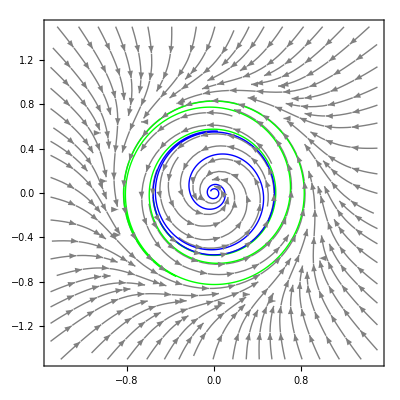

```mathematica
sol1=NDSolve[{x'[t]==-(y[t] (0.1+1/2 (x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(x[t] (-0.215 √(x[t]^2+y[t]^2)+(x[t]^2+y[t]^2)^(3/2)-(x[t]^2+y[t]^2)^(5/2)))/(√(x[t]^2+y[t]^2)),y'[t]==(x[t] (0.1+1/2 (x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(y[t] (-0.215 √(x[t]^2+y[t]^2)+(x[t]^2+y[t]^2)^(3/2)-(x[t]^2+y[t]^2)^(5/2)))/(√(x[t]^2+y[t]^2)),x[1]==1,y[1]==0},{x,y},{t,0,20}];
sol2=NDSolve[{x'[t]==-(y[t] (0.1+1/2 (x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(x[t] (-0.215 √(x[t]^2+y[t]^2)+(x[t]^2+y[t]^2)^(3/2)-(x[t]^2+y[t]^2)^(5/2)))/(√(x[t]^2+y[t]^2)),y'[t]==(x[t] (0.1+1/2 (x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(y[t] (-0.215 √(x[t]^2+y[t]^2)+(x[t]^2+y[t]^2)^(3/2)-(x[t]^2+y[t]^2)^(5/2)))/(√(x[t]^2+y[t]^2)),x[20]==0.7,y[20]==0},{x,y},{t,0,40}];
sol3=NDSolve[{x'[t]==-(y[t] (0.1+1/2 (x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(x[t] (-0.215 √(x[t]^2+y[t]^2)+(x[t]^2+y[t]^2)^(3/2)-(x[t]^2+y[t]^2)^(5/2)))/(√(x[t]^2+y[t]^2)),y'[t]==(x[t] (0.1+1/2 (x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(y[t] (-0.215 √(x[t]^2+y[t]^2)+(x[t]^2+y[t]^2)^(3/2)-(x[t]^2+y[t]^2)^(5/2)))/(√(x[t]^2+y[t]^2)),x[35]==0.1,y[35]==0},{x,y},{t,0,40}];
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{-0.215*r+r^3-r^5,ω+b*r^2},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Gray],ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,0,20},PlotStyle->{Red,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol2],{t,0,40},PlotStyle->{Green,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol3],{t,0,40},PlotStyle->{Blue,Thick}]}]
```

## Bifurcación transcrítica de ciclos

```mathematica
Manipulate[Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*(r-1)-(r-1)^2,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*(r-1)-(r-1)^2,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamPoints->{{-1.5,1.5},{0.2,0}},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamMarkers->"Box"]}],{μ,-1,1}]
```

## Bifurcación de tridente supercrítica de ciclos

```mathematica
Manipulate[Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*(r-1)-(r-1)^3,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*(r-1)-(r-1)^3,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamPoints->{{-1.5,1.5},{0.2,0},{0,1}},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamMarkers->"Box"]}],{μ,-1,1}]
```

## Bifurcación de tridente subcrítica de ciclos

```mathematica
Manipulate[Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*(r-1)+(r-1)^3,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{μ*(r-1)+(r-1)^3,ω+b*r^2},{r,θ}->{x,y}],{x,-2,2},{y,-2,2},StreamPoints->{{-1.5,1.5},{0.2,0},{0,1}},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamMarkers->"Box"]}],{μ,-1,1}]
```

## Bifurcación de período infinito

Un ejemplo es el sistema


Espacio fase de la parte radial:

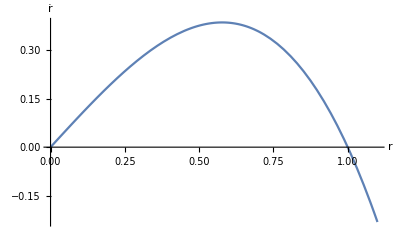

```mathematica
Plot[r*(1-r^2),{r,0,1.1},AxesLabel->{r,OverDot[r]}]
```

Espacio fase de la parte angular:

```mathematica
Manipulate[Plot[μ-Sin[x],{x,0,2*Pi},AxesLabel->{θ,OverDot[θ]},PlotRange->{{0,2*Pi},{-2,3}},Ticks->{{0,Pi/2,Pi,3*Pi/2,2*Pi},Automatic}],{μ,0,2}]
```

En  vemos primero el retrato fase:

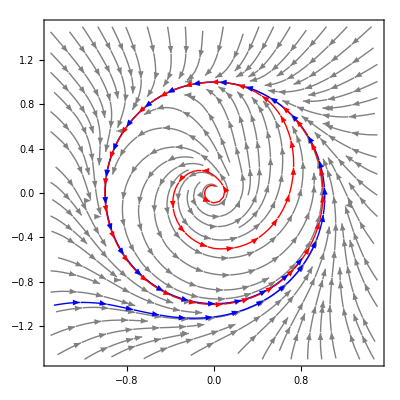

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1.2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Gray],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1.2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Blue,Thick},StreamPoints->{{-1,-1}}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1.2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamPoints->{{0,-1/2}}]}]
```

Y ahora vemos la solución :

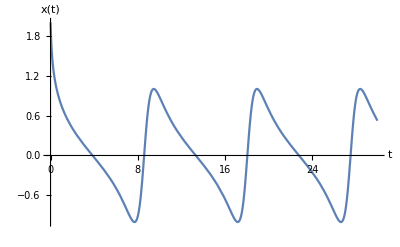

```mathematica
sol4=NDSolve[{r'[t]==r[t]*(1-r[t]^2),θ'[t]==1.2-Sin[θ[t]],r[0]==2,θ[0]==0},{r,θ},{t,0,30}];
Plot[Evaluate[r[t]*Cos[θ[t]]/.sol4],{t,0,30},AxesLabel->{t,x[t]}]
```

Ahora vemos el retrato fase en :

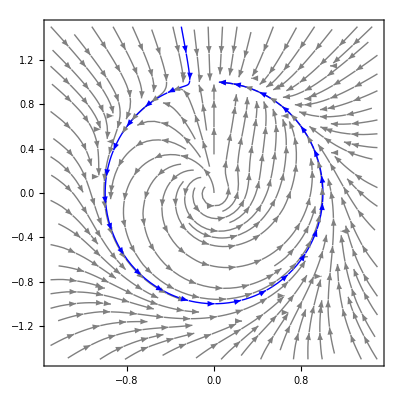

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Gray],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),1-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Blue,Thick},StreamPoints->{{-0.3,1.5}}]}]
```

Y ahora vemos la solución :

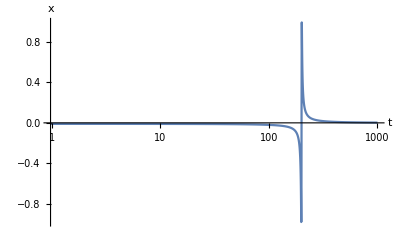

```mathematica
sol5=NDSolve[{r'[t]==r[t]*(1-r[t]^2),θ'[t]==1-Sin[θ[t]],r[0]==1,θ[0]==Pi/2+0.01},{r,θ},{t,0,1000}];
LogLinearPlot[Evaluate[r[t]*Cos[θ[t]]/.sol5],{t,0,1000},AxesLabel->{"t",x},PlotRange->All]
```

Nos acercamos a la oscilación:

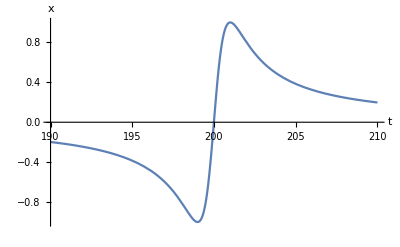

```mathematica
Plot[Evaluate[r[t]*Cos[θ[t]]/.sol5],{t,190,210},AxesLabel->{t,x},PlotRange->All]
```

Ahora vemos qué pasa cuando  en el espacio fase:

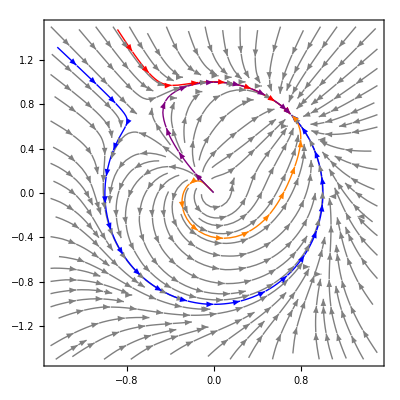

```mathematica
Show[{StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Gray],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Blue,Thick},StreamPoints->{{-1.1,1}}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Red,Thick},StreamPoints->{{-0.5,1}}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Orange,Thick},StreamPoints->{{-0.11,0.1}}],StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),Sqrt[2]/2-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->{Purple,Thick},StreamPoints->{{-0.4,0.5}}]}]
```

Y vemos la solución :

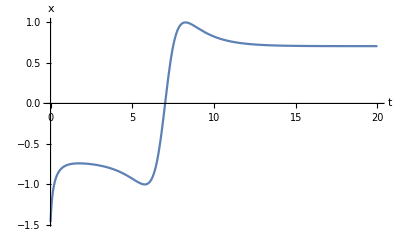

```mathematica
sol6=NDSolve[{r'[t]==r[t]*(1-r[t]^2),θ'[t]==Sqrt[2]/2-Sin[θ[t]],r[0]==2.05,θ[0]==3*Pi/4+0.01},{r,θ},{t,0,20}];
Plot[Evaluate[r[t]*Cos[θ[t]]/.sol6],{t,0,20},AxesLabel->{t,x},PlotRange->All]
```

Finalmente veamos todo el proceso bifurcativo:

```mathematica
Manipulate[StreamPlot[Evaluate@TransformedField["Polar"->"Cartesian",{r*(1-r^2),μ-Sin[θ]},{r,θ}->{x,y}],{x,-1.5,1.5},{y,-1.5,1.5}],{μ,Sqrt[2]/2,1.2}]
```

## Bifurcación homoclínica

Ejemplo:


Primero veamos todo el proceso de bifurcación:

```mathematica
Manipulate[Show[{StreamPlot[{y,μ*y+x-x^2+x*y},{x,-2,2},{y,-2,2}],StreamPlot[{y,μ*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamPoints->{{0.1,0.1*(μ+Sqrt[μ^2+4])/2}},StreamColorFunction->None,StreamStyle->{Red,Thick}]}],{μ,-1,-0.8}]
```

Observamos lo que pasa antes de la bifurcación:

NDSolve::ndsz: At t == 889.009, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {0.00909091} lies outside the range of data in the interpolating function. Extrapolation will be used.

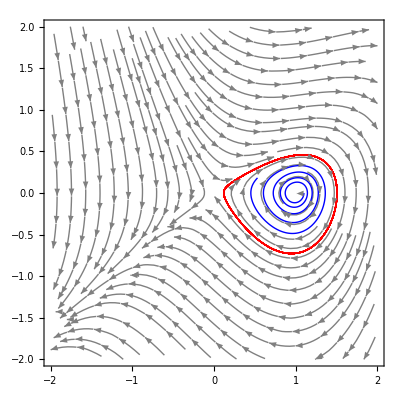

```mathematica
sol7=NDSolve[{x'[t]==y[t],y'[t]==-0.88*y[t]+x[t]-x[t]^2+x[t]*y[t],x[900]==0.01,y[900]==0.01*(-0.88-Sqrt[0.88^2+4])/2},{x,y},{t,0,900}];
sol8=NDSolve[{x'[t]==y[t],y'[t]==-0.88*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.5,y[0]==0},{x,y},{t,0,900}];
sol9=NDSolve[{x'[t]==y[t],y'[t]==-0.88*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==1.1,y[0]==0},{x,y},{t,0,100}];
Show[{StreamPlot[{y,-0.88*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Gray],ParametricPlot[Evaluate[{x[t],y[t]}/.sol8],{t,800,900},PlotPoints->100,PlotStyle->{Red,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol9],{t,0,30},PlotPoints->100,PlotStyle->{Blue,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol7],{t,0,900},PlotPoints->100,PlotStyle->{Black,Thick}]}]
```

Veamos la componente  de la trayectoria azul:

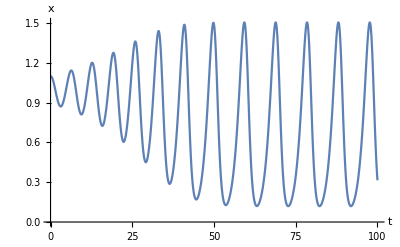

```mathematica
Plot[Evaluate[x[t]/.sol9],{t,0,100},AxesLabel->{t,x}]
```

Ahora veamos el punto de la bifurcación ():

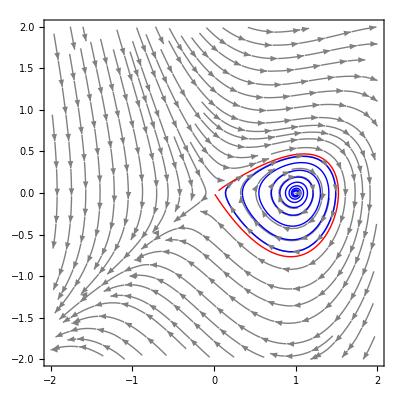

```mathematica
sol10=NDSolve[{x'[t]==y[t],y'[t]==-0.8645*y[t]+x[t]-x[t]^2+x[t]*y[t],x[900]==0.01,y[900]==0.01*(-0.8645-Sqrt[0.8645^2+4])/2},{x,y},{t,0,900}];
sol11=NDSolve[{x'[t]==y[t],y'[t]==-0.8645*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.98,y[0]==0.01},{x,y},{t,0,85}];
Show[{StreamPlot[{y,-0.8645*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Gray],ParametricPlot[Evaluate[{x[t],y[t]}/.sol10],{t,889,900},PlotPoints->100,PlotStyle->{Red,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol11],{t,0,60},PlotPoints->100,PlotStyle->{Blue,Thick}]}]
```

Y observamos la solución  para la trayectoria azul:

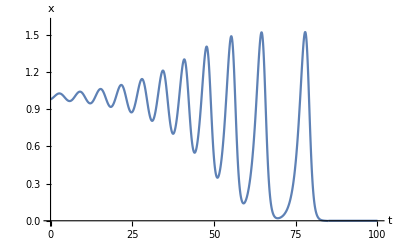

```mathematica
Show[{Plot[Evaluate[x[t]/.sol11],{t,0,85},AxesLabel->{t,x},PlotRange->{{0,100},{-0.01,1.6}}],Plot[0,{t,85,100}]}]
```

Finalmente, veamos qué pasa después de la bifurcación, :

NDSolve::nderr: Error test failure at t == 38.6531; unable to continue.

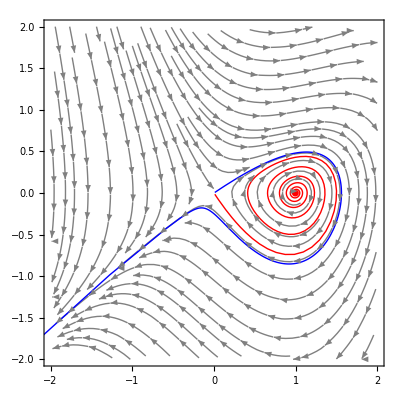

```mathematica
sol12=NDSolve[{x'[t]==y[t],y'[t]==-0.83*y[t]+x[t]-x[t]^2+x[t]*y[t],x[900]==0.01,y[900]==0.01*(-0.83-Sqrt[0.83^2+4])/2},{x,y},{t,0,900}];
sol13=NDSolve[{x'[t]==y[t],y'[t]==-0.83*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.01,y[0]==0.01*(-0.83+Sqrt[0.83^2+4])/2},{x,y},{t,0,100}];
Show[{StreamPlot[{y,-0.83*y+x-x^2+x*y},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Gray],ParametricPlot[Evaluate[{x[t],y[t]}/.sol12],{t,0,900},PlotPoints->100,PlotStyle->{Red,Thick}],ParametricPlot[Evaluate[{x[t],y[t]}/.sol13],{t,0,100},PlotPoints->100,PlotStyle->{Blue,Thick}]}]
```

Y elegimos la solución  de una trayectoria dentro de la espiral:

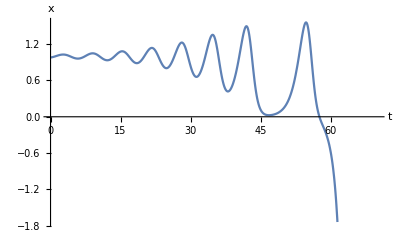

```mathematica
sol14=NDSolve[{x'[t]==y[t],y'[t]==-0.83*y[t]+x[t]-x[t]^2+x[t]*y[t],x[0]==0.98,y[0]==0.01},{x,y},{t,0,70}];
Plot[Evaluate[x[t]/.sol14],{t,0,70},AxesLabel->{t,x}]
```